Routines for YODA plotting

from: https://yoda.hepforge.org/trac/wiki/DataFormat

```mathematica
<<(NotebookDirectory[]<>"../../atom_mathematica.m")
```

```mathematica
Zee=(GetYodaRaw[NotebookDirectory[]<>"Zee.yoda"]);
```

3 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta_inc/0

2 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta/0

1 Imported ..Histo1D..  /ATLAS_1407_5063/Mee/0

This contains Hist1D objects:

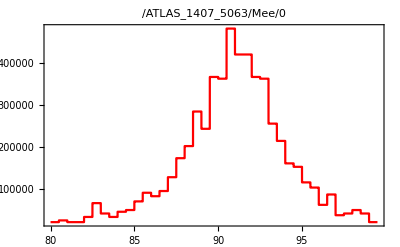

```mathematica
F1=HistogramPlot[Zee[[1]],PlotStyle->{Red}]
```

```mathematica
ATLAS=(GetYodaRaw[NotebookDirectory[]<>"ATLAS_Zee.yoda"]);
```

1 Imported ..Scatter2D..  /REF/ATLAS_1008_2461/d01-x01-y01

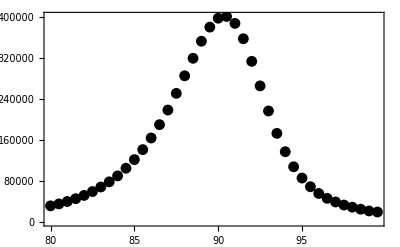

```mathematica
F2=ScatterPlot[ATLAS[[1]],PlotStyle->{Black}]
```

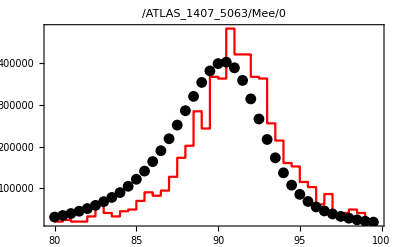

```mathematica
Show[{F1,F2}]
```